# Fully implicit Scheme

## Fully implicit method with expanding space grid

Backward-difference (fully implicit) method for a potential step to the limiting current region for the reaction O+e⇌R.

Version 1.30
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot3D,
AspectRatio-> 1,
AxesLabel->{
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["j",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["c  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Plain,FontWeight-> Bold]},
ImageSize->288,
ViewPoint->{2,-.5,1},
Mesh->False];
```

```mathematica
SetOptions[ListPlot,
Frame->True,
FrameStyle->AbsoluteThickness[1],
GridLines->None,
ImageSize->400,
PlotStyle->{Blue,AbsoluteThickness[1]},
Joined->True];
```

```mathematica
optionA={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None},
FormatType-> TraditionalForm,
Frame-> False,
Joined-> False,
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None,
PlotStyle-> Thickness[0],
Prolog-> {Green,AbsolutePointSize[4.5]}
};
```

```mathematica
optionB={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["z  ",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
None,
None},
FormatType-> TraditionalForm,
Frame-> False,
Joined-> True,
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None,
PlotStyle-> {Red,Thickness[0.002]}};
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeVarDiagonals];

makeVarDiagonals[m_Integer,d_][yLim_,α_]:=
	Module[{x,y,z},
		x=Table[-d*Exp[-2*(j-1)/(m-1)*yLim]*(1+α),{j,3,m-1}];
		z=Table[-d*Exp[-2*(j-1)/(m-1)*yLim]*(1-α),{j,2,m-2}];
		y=Table[1+2*d*Exp[-2*(j-1)/(m-1)*yLim],{j,2,m-1}];

{x,y,z}]
```

```mathematica
makeVarDiagonals[5,𝔻][yLim,α]
```

{{-0.218275,-0.0500757},{2.83533,1.42105,1.0966},{-0.883888,-0.202778}}

## Set Up Solution

### LinearSolve solution

```mathematica
makeMatrix[m_]:=Module[{x,y,z},
{x,y,z}=makeVarDiagonals[m,𝔻][yLim,α];Table[Switch[j-i,-1,x⟦j⟧,0,y⟦j⟧,1,z⟦j-1⟧,_,0],{i,m-2},{j,m-2}]];
makeMatrix[7]//MatrixForm
```

(3.99805 | -1.44385 | 0 | 0 | 0
-0.582445 | 2.12354 | -0.541093 | 0 | 0
0 | -0.218275 | 1.42105 | -0.202778 | 0
0 | 0 | -0.0817998 | 1.15779 | -0.0759922
0 | 0 | 0 | -0.030655 | 1.05913)

```mathematica
Clear[implicitVarSolve];

implicitVarSolve[m_Integer,n_Integer,d_][yLim_,α_]:=Module[{x,y,z,len,mat,initial,solveNext},
{x,y,z}=makeVarDiagonals[m,d][yLim,α];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
initial=ConstantArray[1.,{m}];
solveNext:=Module[{b},
b=#⟦2;;-2⟧;
b[[-1]]=b[[-1]]+d*Exp[-2.*(m-2)/(m-1)*yLim]*(1-α);
Flatten[{0.,LinearSolve[mat,b],1.}]]&;

NestList[solveNext,initial,n-1]]
```

## Set Parameter Values

```mathematica
Clear[n,a,yLim,𝔻,m,𝒟,Δy,α];

n=400;

a=3.;

yLim=Log[1.+6.*a];

𝔻=4.;

m=1+Ceiling[yLim/a*√(𝔻*(n-1))];

𝒟=10^-5 (*diffusion coefficient*);

(*Δy=a*√((𝒟*Δt)/𝔻);*)

α=yLim/(2*(m-1));
```

## Solve

LinearSolve solution

```mathematica
Clear[c];

Timing[
c=implicitVarSolve[m,n,𝔻][yLim,α];
c=Rest[c];]
```

{0.032734,Null}

## Plot Current v. Time

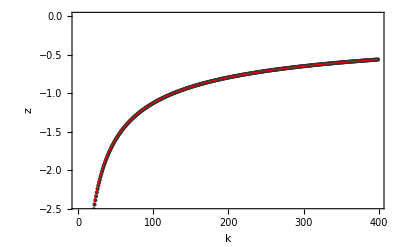

```mathematica
Clear[i,z];
i=Map[((-4*#⟦2⟧+#⟦3⟧)*0.5*√(𝔻*(n-1)))&,c];

z=Table[-1/Sqrt[Pi*(k-1)/(n-1)],{k,2,n-1}]//N;

Show[ListPlot[i,optionA],ListPlot[z,optionB]]
```